```mathematica
Exit[]
```

```mathematica
$Assumptions=μ>0&&σ>0&&a ∈ Reals&&1>k1≥0&&k0≥0&&S0>0&&K>0&&r≥0&&b ∈ Reals&& rf≥0&& γ>0;
```

```mathematica
ost == σ √t; mpr==(μ-r)/σ^2;
xx[W_,mpr_,ost_]:=Exp[ ost W+(mpr-1/2)ost^2];
Δ[k_]:=1/2(1+Erf[(-Log[k]+ost^2/2)/ost])-1//N
Δ[0.]=0;
```

```mathematica
γ=.1;mpr=0.1;ost=.01;
NIntegrate[xx[w,mpr,ost]Exp[-w^2/2],{w,-∞,∞}]/√(2π)-Exp[mpr ost^2]

pr[f_]:=Log[NIntegrate[Exp[-γ f[xx[w,mpr,ost]]-w^2/2],{w,-∞,∞}]/√(2π)]/-γ;
opt2[f_]:=NIntegrate[Exp[-γ f[xx[w,mpr,ost]]-w^2/2](xx[w,mpr,ost]-1),{w,-∞,∞}];
opt[f_]:=Min[.1,Max[-.1,opt2[f]]]

h[a_]:=a(#-1)&
put[k_,a_]:=h[a][#]-Max[0,k-#]&;
```

-6.54587×10^-13

```mathematica
γ=.1;mpr=0.1;ost=1;arb=Quiet[FindRoot[opt2[h[b]]==0,{b,0,10}][[1,2]]]
hedge[k_]:=If[opt2[put[k,0]]≤ 0,0,FindRoot[opt2[put[k,a]]==0,{a,0,10}][[1,2]]]

plot[kl_]:=Module[{x=Quiet[hedge[#]]&/@kl,y,i=1},
y=Max[x];
Show[ParallelTable[With[{j=i++},
Plot[pr[put[k,a]]-put[k,a][1],{a,0,3 y},
PlotStyle->{ColorData[1,"ColorList"][[j]]}
]],{k,kl}],
PlotRange->All,
Epilog->Flatten[{Directive[{Dashed,Red}],
Table[
{Point[{x[[i]],0}],
Point[{x[[i]],pr[put[kl[[i]],x[[i]]]]-put[kl[[i]],x[[i]]][1]}]}
,{i,Length[kl]}]}]
]]
```

0.621583

```mathematica
$Assumptions=k≥ 0&&b>0;
```

```mathematica
ost=.;mpr=.
```

```mathematica
D[f[a,w,b],a]
```

ⅇ^(-a (-1+ⅇ^((-1/2+mpr) ost^2+ost w-b w^2))-w^2/2) (1-ⅇ^((-1/2+mpr) ost^2+ost w-b w^2))

```mathematica
f[a_,w_,b_,t_]:=Exp[-a (ⅇ^((mpr -1/2)t^2+ t w-b w^2)-1)-w^2/2]
df[a_,w_,b_,t_]:=ⅇ^(-a (-1+ⅇ^((-1/2+mpr) t^2+t w-b w^2))-w^2/2) (1-ⅇ^((-1/2+mpr) t^2+t w-b w^2))
g[a_,b_,t_]:=NIntegrate[f[a,w,b,t],{w,-∞,∞}]
dg[a_,b_,t_]:=NIntegrate[df[a,w,b,t],{w,-∞,∞}]
```

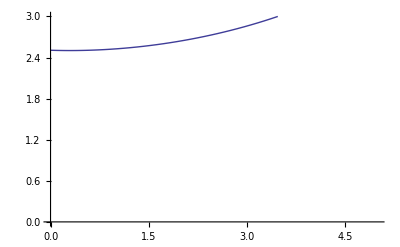

```mathematica
mpr=.3;Plot[g[a,.0,.2],{a,0,5},PlotRange->{0,3}]
```

```mathematica
Normal[Series[df[a,w, 0,t],{t,0,3}]]
```

-ⅇ^(-w^2/2) t w+1/2 ⅇ^(-w^2/2) t^2 (1-2 mpr-w^2+2 a w^2)-1/6 ⅇ^(-w^2/2) t^3 w (-3+6 a+6 mpr-12 a mpr+w^2-6 a w^2+3 a^2 w^2)

```mathematica
Integrate[,{w,-∞,∞}]
```

√(π/2) (2+a t (2 b+3 (-1+a) b^2 t+(a-2 mpr) t))

```mathematica
MinValue[√(π/2) (2+a t (2 b+3 (-1+a) b^2 t+(a-2 mpr) t)),{a}]
```

Piecewise[{{√(2 π), (b>0&&t==0)||(b<0&&t==0)}, {1/4 (4 √(2 π)-2 mpr^2 √(2 π) t^2), b==0}, {1/(4+12 b^2)(4 √(2 π)+10 b^2 √(2 π)+6 b^3 √(2 π) t+4 b mpr √(2 π) t-9 b^4 √(π/2) t^2-6 b^2 mpr √(2 π) t^2-2 mpr^2 √(2 π) t^2), True}}]

```mathematica
Series[%,{t,0,2}]
```

√(2 π)+a b √(2 π) t+(a^2-3 a b^2+3 a^2 b^2-2 a mpr) √(π/2) t^2+O[t]^3

```mathematica
Integrate[SeriesCoefficient[df[a,w, b √t,t],{t,0,2}],{w,-∞,∞}]
```

1/4 (8 a+35 (-1+2 (-1+a) a (-7+2 a)) b^4-8 mpr) √(π/2)

```mathematica
SeriesCoefficient[df[a,w, b,t],{t,0,2}]
```

a ⅇ^(a (1-ⅇ^(-2.4 w^2))-5.3 w^2) w^2-1/2 ⅇ^(a (1-ⅇ^(-2.4 w^2))-2.9 w^2) (-1+2 mpr+w^2)+1/2 ⅇ^(a (1-ⅇ^(-2.4 w^2))-w^2/2) (1-ⅇ^(-2.4 w^2)) (a^2 ⅇ^(-4.8 w^2) w^2-a ⅇ^(-2.4 w^2) (-1+2 mpr+w^2))

```mathematica
1/2 (-1+2 a) ⅇ^(-w^2/2) t^2 w^2-1/6 (1-6 a+3 a^2) ⅇ^(-w^2/2) t^3 w^3
```

1/2 (-1+2 a) ⅇ^(-w^2/2) t^2 w^2-1/6 (1-6 a+3 a^2) ⅇ^(-w^2/2) t^3 w^3

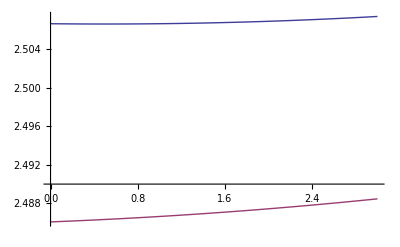

```mathematica
ost=.01;mpr=0.5;b=2.4;o=-0 3;p=3;Plot[{g[Max[0,a],∞],g[a,b]},{a,o,p}]
```

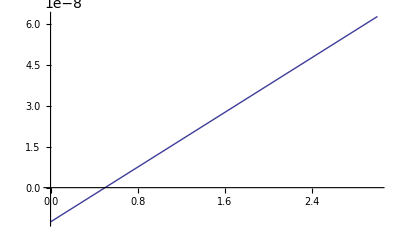

```mathematica
ost=.0001;b=2.4;o=-1 0;p=3;Plot[{dg[Max[0,a],∞]},{a,o,p}]
```

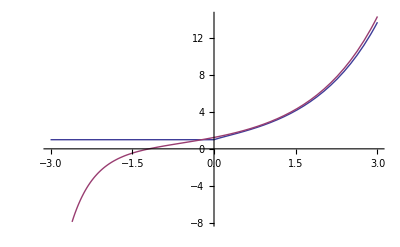

```mathematica
b=.1;o=-3;p=3;Plot[{dg[Max[0,a],0],dg[a,b]},{a,o,p}]
```

```mathematica
h[b_]:=Quiet[FindRoot[dg[a,b]==0,{a,-5,5}][[1,2]]]
```

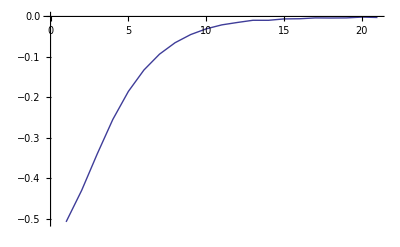

```mathematica
ListLinePlot[Table[h[1/n/2],{n,10,30}]]
```

```mathematica
fcs=Quiet[Table[fc2[n],{n,650}]];
```

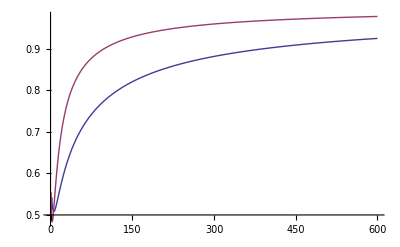

```mathematica
ListLinePlot[Transpose[Table[{Abs[fcs[[n]]]^(1/n),Abs[fcs[[n+1]]/fcs[[n]]]},{n,1,600}]]]
```